```mathematica
ClearAll["Global`*"];
```

```mathematica
F[t_]:=HeavisideTheta[1-t]*Cos[10*t];
```

```mathematica
γ=1;ω=1;
```

```mathematica
s=NDSolve[{x''[t]==-ω^2*x[t]-γ*x'[t]+F[t],x[0]==0,x'[0]==0},x,{t,0,20}]
```

{{x→InterpolatingFunction[…]}}

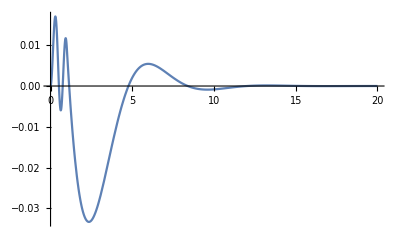

```mathematica
Plot[Evaluate[x[t]/. s],{t,0,20},PlotRange->All]
```